```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/Critical-region/critical_region/LPA/runningpoint/delta

```mathematica
mub=Table[0+i*50,{i,1,14}];
sigma=Table[Flatten[Import["./LPA_hscaling_mub"<>ToString[mub[[i]]]<>"/buffer/fpi.dat"]],{i,1,Length[mub]}];
c=Table[Flatten[Import["./LPA_hscaling_mub"<>ToString[mub[[i]]]<>"/buffer/c.dat"]]*197.33^3,{i,1,Length[mub]}];
mpi=Table[Flatten[Import["./LPA_hscaling_mub"<>ToString[mub[[i]]]<>"/buffer/mPion.dat"]],{i,1,Length[mub]}];
dataLO=Table[Transpose[{Log[c[[i]][[2;;Length[c[[i]]]]]],Log[sigma[[i]][[2;;Length[c[[i]]]]]]}],{i,1,Length[mub]}];
hLO=Table[Transpose[{mpi[[j]][[2;;Length[c[[j]]]-2]],1/Flatten[Table[FindFit[dataLO[[j]][[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[c[[j]]]-2}]]}],{j,1,Length[mub]}];
cphy=1.7*10^6;
sigmaphy=92;
c0=Table[Flatten[c[[i]]/cphy],{i,1,Length[mub]}];
delta0=Table[Flatten[sigma[[i]]/92],{i,1,Length[mub]}];
mpi=Flatten[Import["./pionmass/LPA_hscaling_mub0/buffer/mPion.dat"]];
(*datamub0=Transpose[{Log[c0[[2;;Length[c0]]]],Log[delta0[[2;;Length[c0]]]]}];
h1mub0=Transpose[{mpi[[2;;Length[c0[[1]]]-2]],1/Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[c0[[1]]]-2}]]}];*)
LMax=Length[mpi];
```

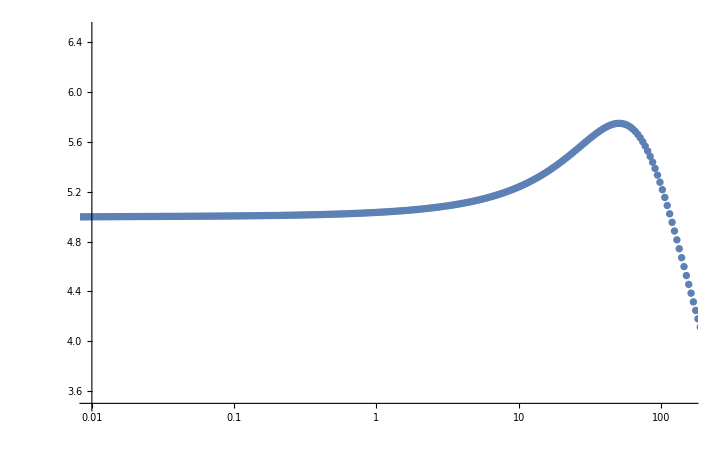

```mathematica
ListPlot[hLO[[1]],ScalingFunctions->{"Log"},PlotRange->{{0.01,150},{3.5,6.5}}]
```

```mathematica
Table[Export["./LOdata/mub"<>ToString[mub[[i]]]<>"data.dat",hLO[[i]]],{i,1,14}]
```

{./LOdata/mub50data.dat,./LOdata/mub100data.dat,./LOdata/mub150data.dat,./LOdata/mub200data.dat,./LOdata/mub250data.dat,./LOdata/mub300data.dat,./LOdata/mub350data.dat,./LOdata/mub400data.dat,./LOdata/mub450data.dat,./LOdata/mub500data.dat,./LOdata/mub550data.dat,./LOdata/mub600data.dat,./LOdata/mub650data.dat,./LOdata/mub700data.dat}

```mathematica
ListΔc3[iMin_,iMax_,l_]:=Table[{c0[[l]][[i]],delta0[[l]][[i]]},{i,iMin,iMax}]
```

```mathematica
delta43=5.`40.;
theta=(0.7878*0.6745)/(0.3989*4.975);
FitRange=Table[160-1(i-1),{i,1,Length[mub]}]
```

{160,159,158,157,156,155,154,153,152,151,150,149,148,147}

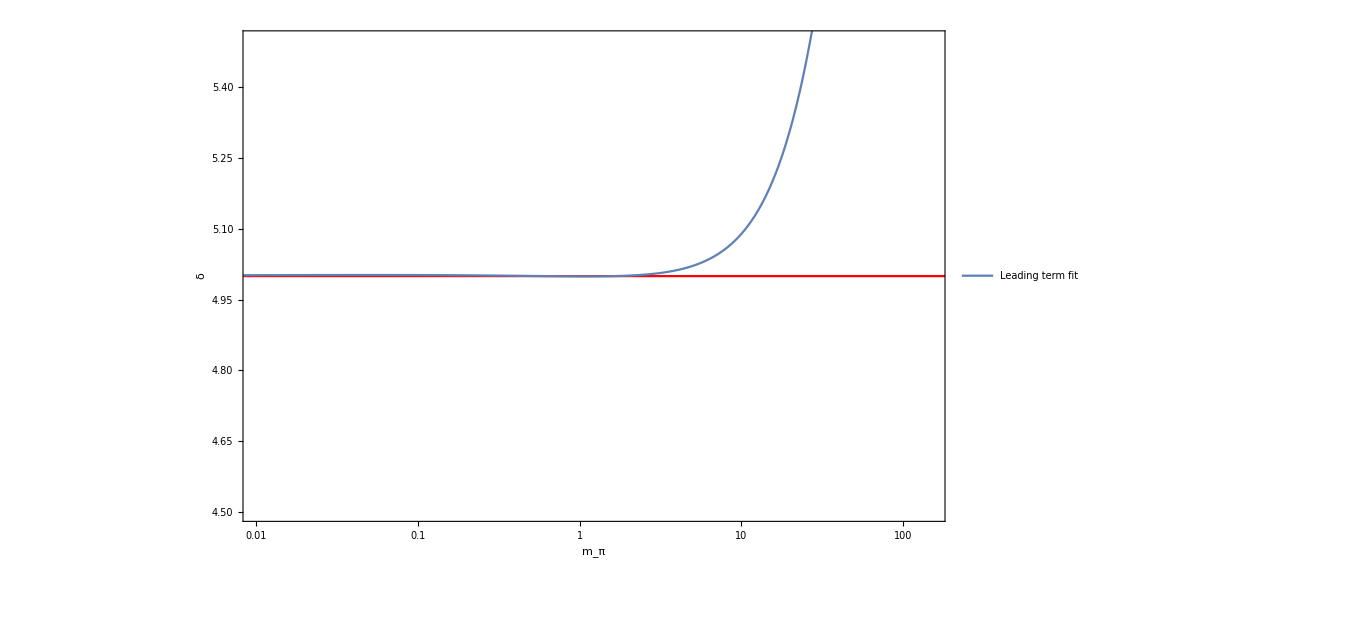

```mathematica
tempfitfab3n2=Table[Block[{Bc12,am12,thetaH=theta},{Bc12,am12}={Bc,am}/.NonlinearModelFit[{Transpose[(SetPrecision[ListΔc3[FitRange[[j]],FitRange[[j]]+17,j],80]//Log)][[1]],Transpose[(SetPrecision[ListΔc3[FitRange[[j]],FitRange[[j]]+17,j],80]//Log)][[2]]}//Transpose,lgbc+Log[1+am ⅇ^(lgx thetaH)]+lgx/delta43,{lgbc,am},lgx,MaxIterations->400]["BestFitParameters"];ParallelTable[Clear[cfa,cfb,na,nb,xadata,xbdata,yadata,ybdata];
{1/invδ,am12,mpi[[i]]}/.NonlinearModelFit[Transpose[{c0[[j]][[i-4;;i+4]]//Log,(SetPrecision[delta0[[j]][[i-4;;i+4]],80]//Log)-Log[1+am12 ⅇ^(Log[SetPrecision[c0[[j]],80]] thetaH)][[i-4;;i+4]]}],lgx*invδ+lgbc,{lgbc,invδ},lgx,MaxIterations->400]["BestFitParameters"],{i,11,296,1}]],{j,1,14(*Length[mub]*)}];
Show[ListLinePlot[{{{0.00001,5},{10^8,5}}},PlotStyle->{Red},ScalingFunctions->{"Log",Automatic},PlotRange->{{0.01,150},{4.5,5.5}},Frame->True,FrameLabel->{"m_π","δ"}],ListLinePlot[Table[tempfitfab3n2[[i]][[All,{3,1}]],{i,13,13,4}],ScalingFunctions->{"Log",Automatic},PlotRange->{{0.0005,1000},{3.5,6.5}},PlotLegends->{"Leading term fit","Subleading term fit"},Frame->True,FrameLabel->{"m_π","δ"}](*,ListLinePlot[hLO[[1]],ScalingFunctions->{"Log",Automatic}]*)]
```